## This file used to be BC_FirstTryTOSS

```mathematica
WantDetails="NoWantDetails";
```

#### Choose Tmat, then check

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatBrownNew;
```

```mathematica
Tmat=TmatDefeat;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatBrownTypo;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

Tmat is TmatSSA2023

A given matrix [T]_𝔹𝔹 is (0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901)

The eigenvalues are: {0.965054,0.701544,0.060227,0.0422136,0.0158499,0.0123903}

The Voigt matrix for the same T is (0.357328 | 0.0423998 | 0.344492 | -0.176408 | -0.0397992 | -0.0419674
0.0423998 | 0.209533 | 0.0934665 | 0.0427684 | -0.0605007 | 0.170826
0.344492 | 0.0934665 | 0.419451 | -0.166206 | -0.0740327 | 0.0186476
-0.176408 | 0.0427684 | -0.166206 | 0.158541 | -0.00329258 | 0.113931
-0.0397992 | -0.0605007 | -0.0740327 | -0.00329258 | 0.03673 | -0.057429
-0.0419674 | 0.170826 | 0.0186476 | 0.113931 | -0.057429 | 0.210212)

#### Specify one of two paths

```mathematica
Σn[0]=TRIV;
Σn[1]=MONO;
Σn[2]=ORTH;
Σn[3]=TET;
Σn[4]=XISO;
Σn[5]=ISO;
nMax=5;
Σn/@Range[0,nMax]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

```mathematica
Σn[0]=TRIV;
Σn[1]=MONO;
Σn[2]=TRIG;
Σn[3]=CUBE;
Σn[4]=ISO;
nMax=4;
Σn/@Range[0,nMax]
```

{TRIV,MONO,TRIG,CUBE,ISO}

#### OutputFor (Pathway 2)

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
OutputFor[Tmat,Σn[#]]&/@Range[0,nMax]
```

Tmat is TmatSSA2023

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

10-6-2023 18:34

𝒯_TRIV = 𝒯

d(T, 𝒯_TRIV) = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯_TRIV) = 0           ''

10-6-2023 18:34

NMinimize = {0.221763,{θ→0.308498,σ→0.601871,ϕ→0.955228}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {17.7,0.,54.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.550163 | -0.303627 | 0.777902
0.175321 | 0.952791 | 0.247895
-0.816445 | 0 | 0.577423)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-6-2023 18:34

NMinimize = {0.538924,{θ→1.2885,σ→-1.80975,ϕ→1.15718}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {73.8,-103.7,66.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.906631 | 0.336094 | 0.25507
-0.362009 | 0.30912 | 0.879428
0.216724 | -0.889655 | 0.401927)  (A TRIG-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

10-6-2023 18:35

NMinimize = {0.723426,{θ→1.21342,σ→-2.01961,ϕ→1.15911}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {69.5,-115.7,66.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.783297 | 0.532604 | 0.320592
-0.477834 | 0.185962 | 0.858541
0.397645 | -0.825682 | 0.400159)  (A CUBE-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

10-6-2023 18:35

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 0.86278   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.806 = 46.19^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (0.229654 | 0. | 0. | 0. | 0. | 0.
0. | 0.229654 | 0. | 0. | 0. | 0.
0. | 0. | 0.229654 | 0. | 0. | 0.
0. | 0. | 0. | 0.229654 | 0. | 0.
0. | 0. | 0. | 0. | 0.229654 | 0.
0. | 0. | 0. | 0. | 0. | 0.64901)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.139785 and μ = 0.114827, Poisson is 0.274506

{Null,Null,Null,Null,Null}

#### OutputFor (Pathway 3) ClosestToPrevious[n, Tmat] has symmetry Σn[n].

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
OutputFor[ClosestToPrevious[#,Tmat],Σn[#+1]]&/@Range[0,nMax-1]
```

Tmat is TmatSSA2023

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

10-6-2023 18:35

NMinimize = {0.221763,{θ→0.308498,σ→0.601871,ϕ→0.955228}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {17.7,0.,54.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.550163 | -0.303627 | 0.777902
0.175321 | 0.952791 | 0.247895
-0.816445 | 0 | 0.577423)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

10-6-2023 18:35

NMinimize = {0.572199,{θ→0.6137,σ→-1.32294,ϕ→2.50355}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {35.2,-75.8,143.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.397192 | -0.777902 | 0.486937
-0.906028 | -0.247895 | 0.343018
-0.146125 | -0.577423 | -0.803262)  (A TRIG-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

10-6-2023 18:35

NMinimize = {0.542337,{θ→1.27239,σ→1.89334,ϕ→0.37168}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {72.9,108.5,21.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.993346 | 0.0431721 | 0.106773
-0.00344589 | -0.93781 | 0.347131
0.115119 | 0.344453 | 0.931719)  (A CUBE-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

10-6-2023 18:35

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 0.271422   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.317 = 18.16^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (0.229654 | 0. | 0. | 0. | 0. | 0.
0. | 0.229654 | 0. | 0. | 0. | 0.
0. | 0. | 0.229654 | 0. | 0. | 0.
0. | 0. | 0. | 0.229654 | 0. | 0.
0. | 0. | 0. | 0. | 0.229654 | 0.
0. | 0. | 0. | 0. | 0. | 0.64901)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.139785 and μ = 0.114827, Poisson is 0.274506

{Null,Null,Null,Null}

#### Elastic maps at the nodes on Pathway 3

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Chop[MatrixForm[ClosestToPrevious[#,Tmat]],0.0001]&/@Range[0,nMax]
```

Tmat is TmatSSA2023

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

{(0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901),(0.304531 | -0.0444525 | 0.238839 | 0.184171 | 0.0910856 | -0.181699
-0.0444525 | 0.101994 | -0.162948 | -0.0406421 | 0.0311181 | -0.146695
0.238839 | -0.162948 | 0.447641 | 0.195593 | 0.00627892 | 0.179027
0.184171 | -0.0406421 | 0.195593 | 0.19617 | 0.0734069 | -0.0951994
0.0910856 | 0.0311181 | 0.00627892 | 0.0734069 | 0.0979336 | -0.184171
-0.181699 | -0.146695 | 0.179027 | -0.0951994 | -0.184171 | 0.64901),(0.204382 | -0.0311103 | 0.0733024 | 0.125232 | 0.0714138 | -0.15935
-0.0311103 | 0.274887 | 0.051893 | -0.119979 | 0.000642399 | -0.226207
0.0733024 | 0.051893 | 0.385686 | 0.00590279 | -0.0443999 | 0.0965977
0.125232 | -0.119979 | 0.00590279 | 0.184002 | 0.0560389 | -0.0345397
0.0714138 | 0.000642399 | -0.0443999 | 0.0560389 | 0.0993116 | -0.156213
-0.15935 | -0.226207 | 0.0965977 | -0.0345397 | -0.156213 | 0.64901),(0.225216 | -0.0135865 | -0.0124208 | 0.0614039 | 0.104043 | 0
-0.0135865 | 0.317269 | -0.00133488 | -0.0338804 | 0.0371691 | 0
-0.0124208 | -0.00133488 | 0.327264 | 0.00863897 | 0.0117662 | 0
0.0614039 | -0.0338804 | 0.00863897 | 0.111249 | 0.0398601 | 0
0.104043 | 0.0371691 | 0.0117662 | 0.0398601 | 0.167271 | 0
0 | 0 | 0 | 0 | 0 | 0.64901),(0.229654 | 0 | 0 | 0 | 0 | 0
0 | 0.229654 | 0 | 0 | 0 | 0
0 | 0 | 0.229654 | 0 | 0 | 0
0 | 0 | 0 | 0.229654 | 0 | 0
0 | 0 | 0 | 0 | 0.229654 | 0
0 | 0 | 0 | 0 | 0 | 0.64901)}

#### Elastic maps at the nodes on Pathway 2

```mathematica
SmatOfN[n_,pw2]:=Closest[Tmat,Σn[n]];
```

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Chop[MatrixForm[SmatOfN[#,pw2]],0.0001]&/@Range[0,nMax]
```

Tmat is TmatSSA2023

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

{(0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901),(0.304531 | -0.0444525 | 0.238839 | 0.184171 | 0.0910856 | -0.181699
-0.0444525 | 0.101994 | -0.162948 | -0.0406421 | 0.0311181 | -0.146695
0.238839 | -0.162948 | 0.447641 | 0.195593 | 0.00627892 | 0.179027
0.184171 | -0.0406421 | 0.195593 | 0.19617 | 0.0734069 | -0.0951994
0.0910856 | 0.0311181 | 0.00627892 | 0.0734069 | 0.0979336 | -0.184171
-0.181699 | -0.146695 | 0.179027 | -0.0951994 | -0.184171 | 0.64901),(0.298984 | 0.074468 | 0.147469 | 0.250236 | 0.121495 | -0.162984
0.074468 | 0.134175 | -0.00379373 | 0.096981 | -0.0011167 | -0.0472721
0.147469 | -0.00379373 | 0.222861 | 0.15267 | 0.0324007 | -0.103433
0.250236 | 0.096981 | 0.15267 | 0.307246 | 0.0816162 | -0.163308
0.121495 | -0.0011167 | 0.0324007 | 0.0816162 | 0.185004 | -0.0685998
-0.162984 | -0.0472721 | -0.103433 | -0.163308 | -0.0685998 | 0.64901),(0.210519 | 0.0449915 | 0.12916 | 0.141359 | 0.0592558 | 0
0.0449915 | 0.321383 | -0.107148 | 0.0304399 | 0.170988 | 0
0.12916 | -0.107148 | 0.251677 | 0.126226 | -0.0389638 | 0
0.141359 | 0.0304399 | 0.126226 | 0.189481 | 0.0480057 | 0
0.0592558 | 0.170988 | -0.0389638 | 0.0480057 | 0.175208 | 0
0 | 0 | 0 | 0 | 0 | 0.64901),(0.229654 | 0 | 0 | 0 | 0 | 0
0 | 0.229654 | 0 | 0 | 0 | 0
0 | 0 | 0.229654 | 0 | 0 | 0
0 | 0 | 0 | 0.229654 | 0 | 0
0 | 0 | 0 | 0 | 0.229654 | 0
0 | 0 | 0 | 0 | 0 | 0.64901)}

#### Elastic maps for the nodes on Pathway 3

```mathematica
SmatOfN[n_,pw3]:=ClosestToPrevious[n,Tmat];
```

```mathematica
Chop[MatrixForm[SmatOfN[#,pw3]],0.0001]&/@Range[0,nMax]
```

{(0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901),(0.304531 | -0.0444525 | 0.238839 | 0.184171 | 0.0910856 | -0.181699
-0.0444525 | 0.101994 | -0.162948 | -0.0406421 | 0.0311181 | -0.146695
0.238839 | -0.162948 | 0.447641 | 0.195593 | 0.00627892 | 0.179027
0.184171 | -0.0406421 | 0.195593 | 0.19617 | 0.0734069 | -0.0951994
0.0910856 | 0.0311181 | 0.00627892 | 0.0734069 | 0.0979336 | -0.184171
-0.181699 | -0.146695 | 0.179027 | -0.0951994 | -0.184171 | 0.64901),(0.204382 | -0.0311103 | 0.0733024 | 0.125232 | 0.0714138 | -0.15935
-0.0311103 | 0.274887 | 0.051893 | -0.119979 | 0.000642399 | -0.226207
0.0733024 | 0.051893 | 0.385686 | 0.00590279 | -0.0443999 | 0.0965977
0.125232 | -0.119979 | 0.00590279 | 0.184002 | 0.0560389 | -0.0345397
0.0714138 | 0.000642399 | -0.0443999 | 0.0560389 | 0.0993116 | -0.156213
-0.15935 | -0.226207 | 0.0965977 | -0.0345397 | -0.156213 | 0.64901),(0.225216 | -0.0135865 | -0.0124208 | 0.0614039 | 0.104043 | 0
-0.0135865 | 0.317269 | -0.00133488 | -0.0338804 | 0.0371691 | 0
-0.0124208 | -0.00133488 | 0.327264 | 0.00863897 | 0.0117662 | 0
0.0614039 | -0.0338804 | 0.00863897 | 0.111249 | 0.0398601 | 0
0.104043 | 0.0371691 | 0.0117662 | 0.0398601 | 0.167271 | 0
0 | 0 | 0 | 0 | 0 | 0.64901),(0.229654 | 0 | 0 | 0 | 0 | 0
0 | 0.229654 | 0 | 0 | 0 | 0
0 | 0 | 0.229654 | 0 | 0 | 0
0 | 0 | 0 | 0.229654 | 0 | 0
0 | 0 | 0 | 0 | 0.229654 | 0
0 | 0 | 0 | 0 | 0 | 0.64901)}

#### The closest ISO is the same for all maps (and same as closest ISO to TRIV).

```mathematica
(* Tset =SmatOfN[#,pw3]&/@Range[1,nMax-1];
MatrixForm[#]&/@Tset
OutputFor[#,ISO]&/@Tset *)
```

#### Angle between the elastic maps at adjacent nodes.

```mathematica
AngleToNextFrom[n_,Tmat_,pw_]:=AngleMatrix[SmatOfN[n+1,pw],SmatOfN[n,pw]]
```

#### Examples.

```mathematica
AngleToNextFrom[#,Tmat,pw2]/Degree&/@Range[0,nMax-2]
```

{10.6898,33.9447,32.7677}

```mathematica
AngleToNextFrom[#,Tmat,pw3]/Degree&/@Range[0,nMax-1]
```

{10.6898,29.1479,31.9098,18.1576}

```mathematica
yy[0,Tmat_,pw_]:=0;
yy[n_,Tmat_,pw_]:=yy[n-1,Tmat,pw]+AngleToNextFrom[n-1,Tmat,pw];
```

```mathematica
ydiff[n_,Tmat_]:=yy[n,Tmat,pw2]-yy[n,Tmat,pw3]
dymax=Max[ydiff[#,Tmat]&/@Range[0,nMax]]
```

0.298412

#### Examples.

```mathematica
yy[#,Tmat,pw2]/Degree&/@Range[0,nMax]
```

{0,10.6898,44.6345,77.4022,107.003}

```mathematica
yy[#,Tmat,pw3]/Degree&/@Range[0,nMax]
```

{0,10.6898,39.8377,71.7475,89.9051}

```mathematica
ydiff[#,Tmat]/Degree&/@Range[0,nMax]
```

{0,0.,4.79683,5.65472,17.0977}

```mathematica
WantPW3="WantPW3"
```

WantPW3

```mathematica
(* WantPW3="NoWantPW3" *)
```

## What is needed here is to generalize the code so that the colors of the Pathway 1 segments are always the same (see hue definitions. See BC_SuperLattice for how this was done by defining BetaCurve[].

Tmat is TmatSSA2023

Node sequence is {TRIV,MONO,TRIG,CUBE,ISO}

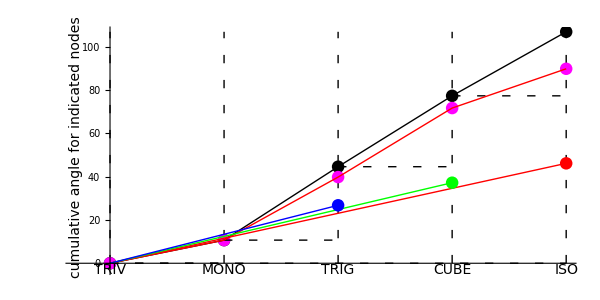

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@Range[0,nMax]];
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],Line[{{0,0},{nMax,0}}],
Table[Line[{{n,0},{n,yy[nMax,Tmat,pw2]/Degree}}],{n,0,nMax}]},     (* vertical dashed lines *)
Point[{#,yy[#,Tmat,pw2]/Degree}]&/@Range[0,nMax],   (* pw2 *)
If[WantPW3=="WantPW3",
{Magenta,PointSize[.015],Point[{#,yy[#,Tmat,pw3]/Degree}]&/@Range[0,nMax]}], (* pw3 *)
{Dashing[{.01,.02}],         (* horizontal dashed steps, pw2 only*)
Line[{{#,      yy[#,Tmat,pw2]/Degree},
   {#+1,yy[#,Tmat,pw2]/Degree}}]&/@Range[0,nMax-1]},
 Line[{#,yy[#,Tmat,pw2]/Degree}&/@Range[0,nMax]],      (* the main polygonal line, pw2 *)
If[WantPW3=="WantPW3",
{Red,Line[{#,yy[#,Tmat,pw3]/Degree}&/@Range[0,nMax]]}],  (* the main polygonal line, pw3 *)
(* this is for MONO-TRIG-CUBE *)
If[True,{
{Red,        Line[{{0,0},{4,AngleMatrix[Tmat,Closest[Tmat,ISO]  ]/Degree}}],Point[{4,AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree}]},
{Green,   Line[{{0,0},{3,AngleMatrix[Tmat,Closest[Tmat,CUBE]]/Degree}}],Point[{3,AngleMatrix[Tmat,Closest[Tmat,CUBE]]/Degree}]},
{Blue,     Line[{{0,0},{2,AngleMatrix[Tmat,Closest[Tmat,TRIG  ]]/Degree}}],Point[{2,AngleMatrix[Tmat,Closest[Tmat,TRIG  ]]/Degree}]}}],
(* this is for MONO-ORTH-TET-XISO *)
If[False,{
{Red,        Line[{{0,0},{5,AngleMatrix[Tmat,Closest[Tmat,ISO]  ]/Degree}}],Point[{5,AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree}]},
{Green,   Line[{{0,0},{4,AngleMatrix[Tmat,Closest[Tmat,XISO]]/Degree}}],Point[{4,AngleMatrix[Tmat,Closest[Tmat,XISO]]/Degree}]},
{Blue,     Line[{{0,0},{3,AngleMatrix[Tmat,Closest[Tmat,TET  ]]/Degree}}],Point[{3,AngleMatrix[Tmat,Closest[Tmat,TET  ]]/Degree}]},
{Orange,Line[{{0,0},{2,AngleMatrix[Tmat,Closest[Tmat,ORTH]]/Degree}}],Point[{2,AngleMatrix[Tmat,Closest[Tmat,ORTH]]/Degree}]}}],
Text[Style[Σn[#],14],{#,-3}]&/@Range[0,nMax],
Text[Style["cumulative angle for indicated nodes",14],{-.3,.5yy[nMax,Tmat,pw2]/Degree},{0,0},{0,1}]},AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},AxesOrigin->{0,0}]
```

#### Difference between Pathway 2 and 3

Tmat is TmatSSA2023

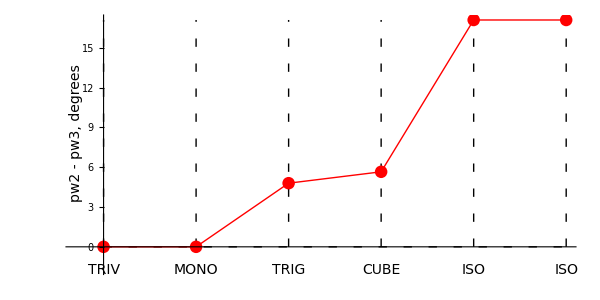

```mathematica
MatrixNote[Tmat]
Graphics[{
{Dashing[{.01,.02}],Line[{{0,0},{5,0}}],Table[Line[{{n,0},{n,dymax/Degree}}],{n,0,5}]},
{Red,PointSize[.015],Point[{#,ydiff[#,Tmat]/Degree}]&/@Range[0,5]}, (* points *)
{Red,Line[{#,ydiff[#,Tmat]/Degree}&/@Range[0,5]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax/Degree}]&/@Range[0,5],
Text[Style["pw2 - pw3, degrees",14],{-.3,.5dymax/Degree},{0,0},{0,1}]},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> False,AxesOrigin->{0,0}]
```

## For comparison

Tmat is TmatBrownTypo

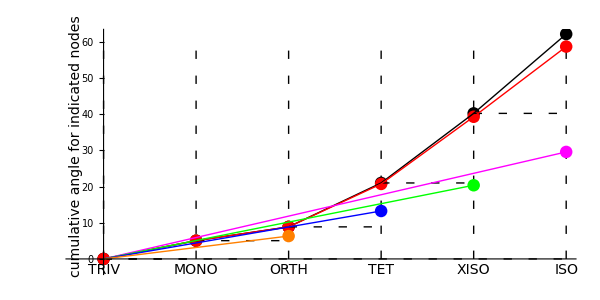

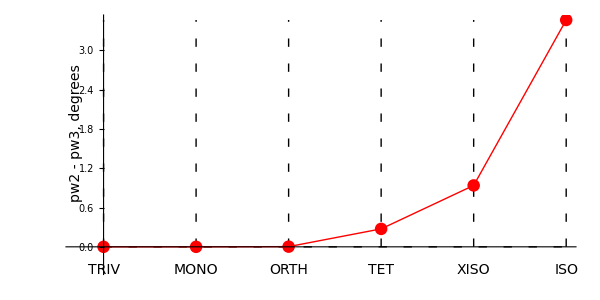

Tmat is TmatBrownNew

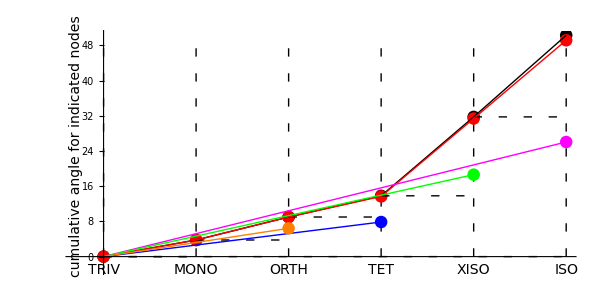

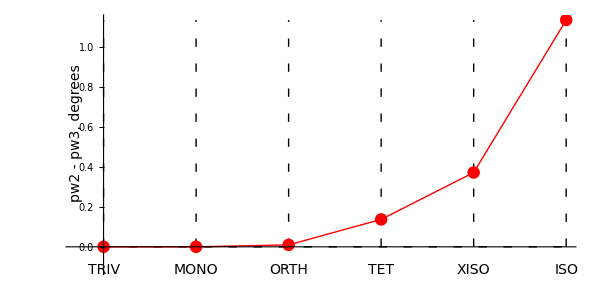

Tmat is TmatSSA2023

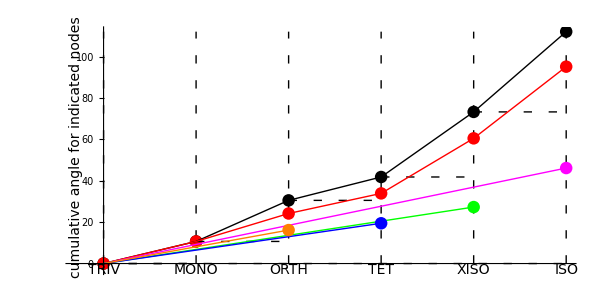

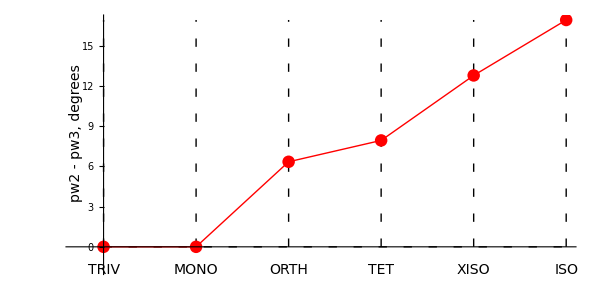

Tmat is TmatDefeat

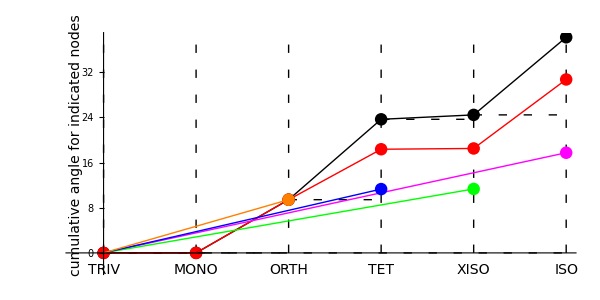

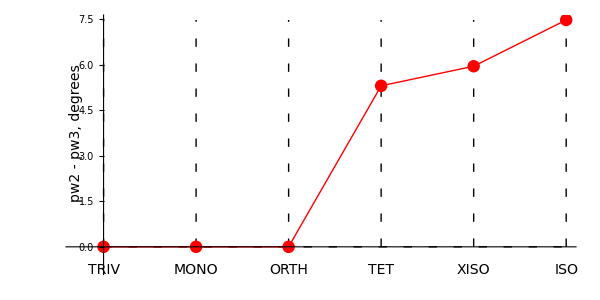

Tmat is TmatMar17

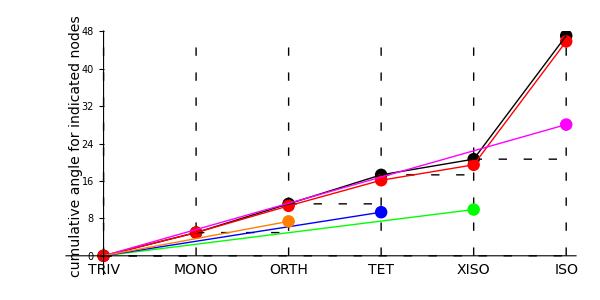

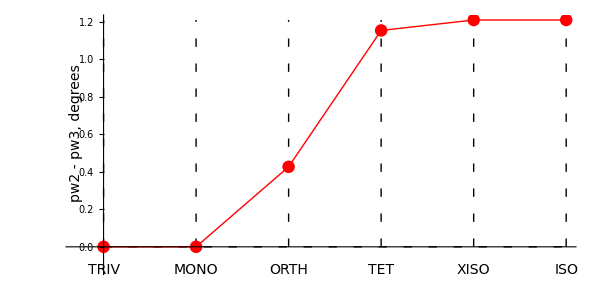

Tmat is TmatIgel